# Sistemas reversibles

## Ejemplo 1:

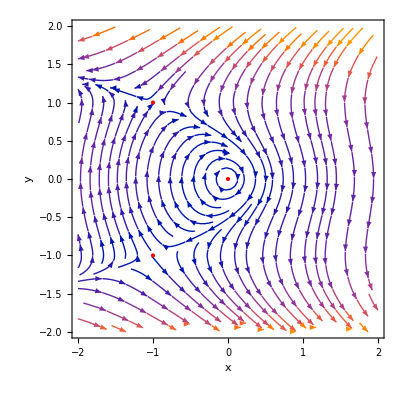

```mathematica
StreamPlot[{y-y^3,-x-y^2},{x,-2,2},{y,-2,2},FrameLabel->{x,y},Epilog->{PointSize[Large],Red,Point[{{0,0},{-1,1},{-1,-1}}]}]
```

## Ejercicio 2:

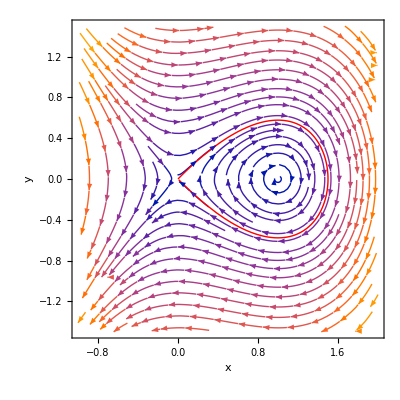

```mathematica
homcl=NDSolve[{x'[t]==y[t],y'[t]==x[t]-x[t]^2,x[0]==1*10^(-5),y[0]==1*10^(-5)},{x,y},{t,0,55}];
Show[{StreamPlot[{y,x-x^2},{x,-1,2},{y,-1.5,1.5},FrameLabel->{x,y}],ParametricPlot[Evaluate[{x[t],y[t]}/.homcl],{t,0,20},PlotStyle->{Red,Thick}]}]
```

## Ejercicio 3:

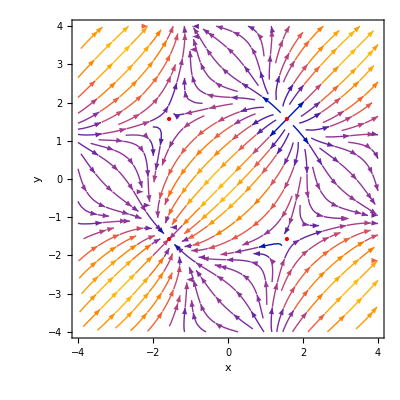

```mathematica
StreamPlot[{-2*Cos[x]-Cos[y],-2*Cos[y]-Cos[x]},{x,-4,4},{y,-4,4},FrameLabel->{x,y},Epilog->{PointSize[Large],Red,Point[{{Pi/2,Pi/2},{-Pi/2,Pi/2},{-Pi/2,-Pi/2},{Pi/2,-Pi/2}}]}]
```